Metric | Original (Q6) | Reduced (negRisk)
Vertices | 64 | 40
Edges | 192 | 150
Diameter | 6 | 5
AverageShortestPath | 64/21 | 901/390
AverageDegree | 6 | 15/2
BipartiteQ | True | False
TriangleCount | 0 | 120

Original (Q6)Reduced (negRisk)

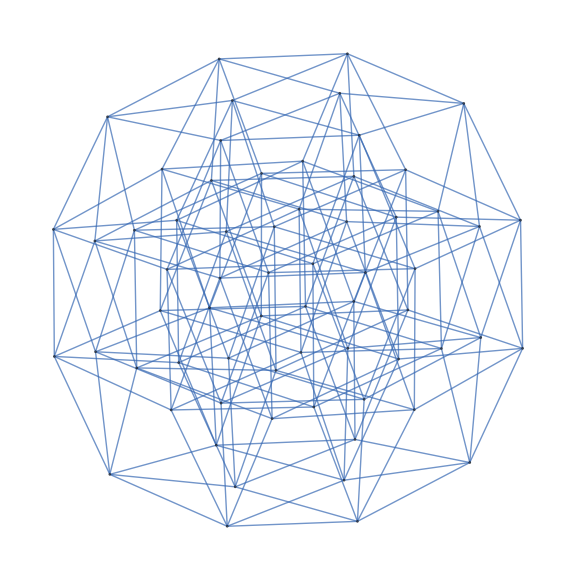
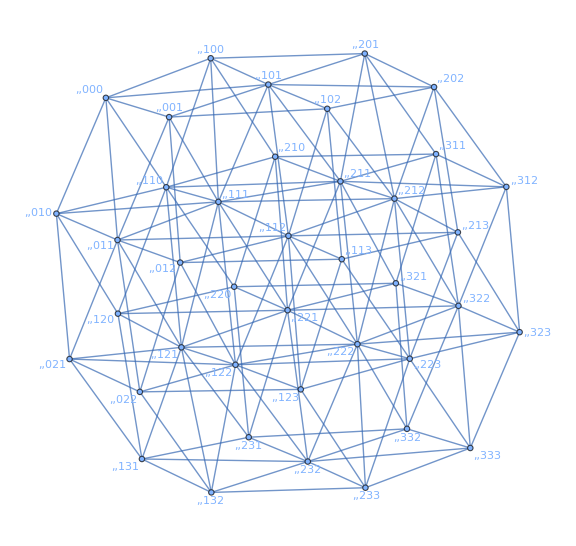

```mathematica
(*-----Full state graph on 6 bits (AY,AN,BY,BN,CY,CN)-----*)states=Tuples[{0,1},6];

hamming1Q[{u_,v_}]:=Total@Abs[u-v]==1;
edges=UndirectedEdge@@@Select[Subsets[states,{2}],hamming1Q];

G=Graph[states,edges,VertexSize->Tiny,ImageSize->Large,GraphLayout->"SpringElectricalEmbedding"];

(*-----negRisk map:NO->complementary YES basket-----*)
(*AN->BY+CY;BN->AY+CY;CN->AY+BY*)
negRisk[{ay_,an_,by_,bn_,cy_,cn_}]:={ay+bn+cn,(*pays on A*)by+an+cn,(*pays on B*)cy+an+bn   (*pays on C*)};

labels=AssociationThread[states,negRisk/@states];

(*-----Build reduced vertices and edges (quotient)-----*)

Vred=Union[Values[labels]];

(*Correct handling of edge endpoints:use (List@@e) in parentheses and drop self-loops when both endpoints map to the same class.*)
Ered=Union@Cases[edges,e_:>Module[{u,v,a,b},{u,v}=(List@@e);
a=labels[u];b=labels[v];
If[a===b,Nothing,UndirectedEdge@@Sort[{a,b}]]]];

Greduced=Graph[Vred,Ered,VertexLabels->(v_:>Row[v,","]),VertexSize->Small,ImageSize->Large,GraphLayout->"SpringElectricalEmbedding"];

(*-----Metrics (robust to older versions)-----*)

avgShortestPath[g_Graph]:=Module[{d=Normal@GraphDistanceMatrix[g],n,vals},n=Length[d];
vals=Flatten@Table[d[[i,j]],{i,1,n-1},{j,i+1,n}];
Mean[vals]];

triangleCount[g_Graph]:=Module[{A=Normal@AdjacencyMatrix[g]},Round[Tr[MatrixPower[A,3]]/6]];

metrics[g_Graph]:=<|"Vertices"->VertexCount[g],"Edges"->EdgeCount[g],"Diameter"->GraphDiameter[g],"AverageShortestPath"->avgShortestPath[g],"AverageDegree"->Mean@VertexDegree[g],"BipartiteQ"->BipartiteGraphQ[g],"TriangleCount"->triangleCount[g]|>;

mFull=metrics[G];
mRed=metrics[Greduced];

metricOrder={"Vertices","Edges","Diameter","AverageShortestPath","AverageDegree","BipartiteQ","TriangleCount"};
Grid[Prepend[(With[{k=#},{k,mFull[k],mRed[k]}]&/@metricOrder),{"Metric","Original (Q6)","Reduced (negRisk)"}],Frame->All]

Row[{Style["Original (Q6)",Bold,14],Spacer[20],Style["Reduced (negRisk)",Bold,14]}]
Row[{G,Greduced}]
```